# One Postulate in Wolfram

This notebook is a public-facing computational companion to the local paper and Lean development. It follows the paper's argument closely enough that a reader can feel why one branch survives, while still keeping Lean as the proof authority.

## What this notebook is for

Question. What is this notebook trying to make visible?

The goal is not to recreate every Lean proof step and not to turn the paper into a static summary card deck. The goal is to make the paper's dynamic claims visible: the kappa-dependent transformation law, the self-test supplied by the Killing form, the loss of a natural ruler at kappa = 0, and the emergence of finite invariant speed and Lorentzian causal structure only for kappa > 0.

All mathematical and proof claims come from local repository files. Wolfram computes exact expressions and interactive views; the paper supplies the narrative; Lean supplies the proof authority.

Answer. This notebook is a computational companion: exact where it should be, public-facing in its presentation, and explicit about what belongs to Wolfram, to the paper, and to Lean.

## The postulate

Question. What kind of explanation does the relativity principle allow?

Einstein's first postulate is treated here as a design principle: no hidden background structure should do the conceptual work that the symmetry rules themselves ought to do. The notebook therefore starts with the one-parameter family and delays geometric interpretation until the algebra has tested itself.

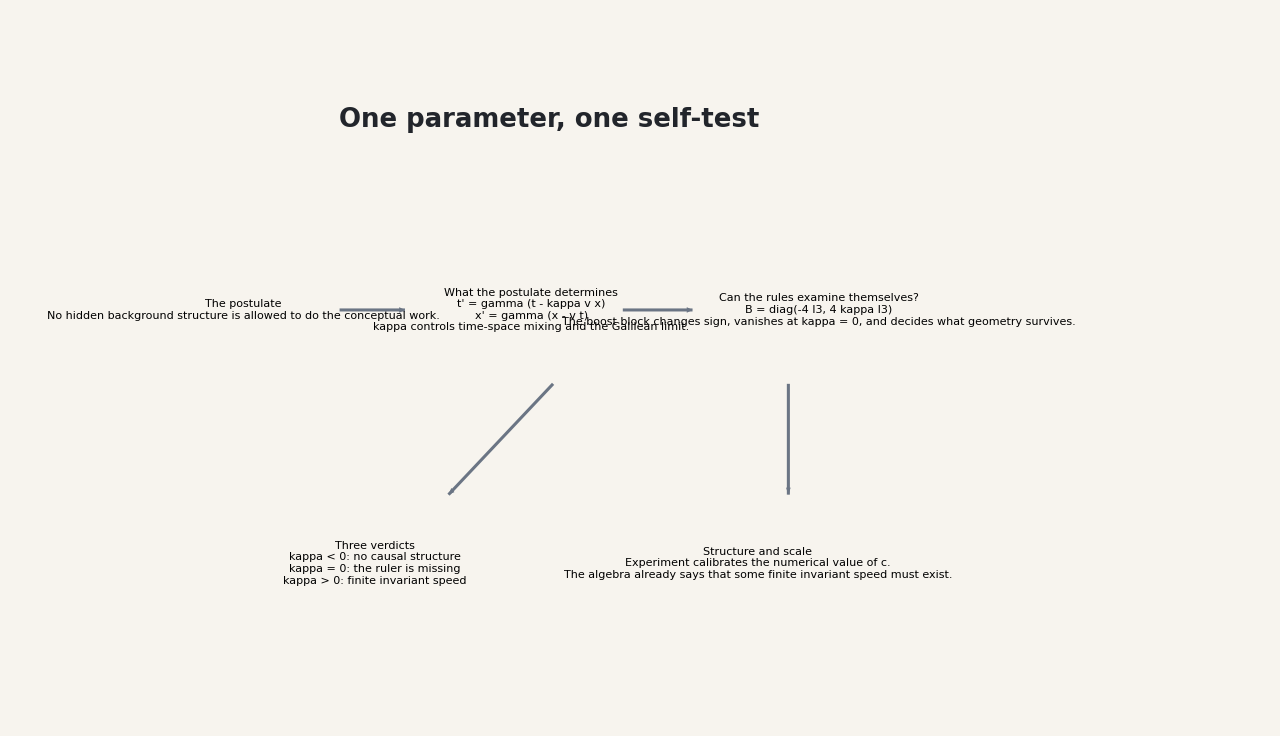
Computed herePaper narrativeLean: matrix_bracket_JJ + matrix_bracket_JK + matrix_bracket_KK
Hero overview
-Graphics-
The narrative arc matches the paper: one parameter controls the family, the Killing form performs the self-test, the three verdicts follow, and experiment calibrates value rather than existence.

Answer. The postulate allows only a self-contained explanation: external measurement may calibrate a scale later, but it should not choose the underlying geometric branch.

## What the postulate determines

Question. What changes when kappa changes sign or magnitude?

The transformation law already contains the full one-parameter family. The second equation shifts position by relative motion; the first mixes space into time with strength set by kappa. When kappa = 0, the mixing vanishes and Newtonian time returns. When kappa > 0, gamma diverges as |v| approaches 1/Sqrt[kappa].

```mathematica
1/(√(1-kappa v^2))
```

1/(√(1-kappa v^2))

```mathematica
(t-kappa v x)/(√(1-kappa v^2))
```

(t-kappa v x)/(√(1-kappa v^2))

```mathematica
(-t v+x)/(√(1-kappa v^2))
```

(-t v+x)/(√(1-kappa v^2))

```mathematica
1
```

1

```mathematica
{t,-t v+x}
```

{t,-t v+x}

Computed herePaper narrativeLean: matrix_bracket_JJ + matrix_bracket_JK + matrix_bracket_KK + phase1_selection_summary
Shared exploration suite

Use the continuous kappa control, velocity slider, draggable event, and tabbed views to move between the three kinematic regimes without leaving the notebook.

Answer. One parameter controls the entire family: it changes the strength of time-space mixing, governs the Galilean limit, and determines whether a finite invariant speed can appear at all.

## Can the rules examine themselves?

Question. Can the algebra diagnose its own geometry without experiment?

Yes. The notebook follows the paper's answer: rotations and boosts are first treated as generators with a bracket structure, and the Killing form then computes the algebra's own diagnostic before any final spacetime metric is read off. The boost block is where the family distinguishes itself.

Computed herePaper narrativeLean: kinematic_bracket_table + boostCommutator_scales_with_kappa
Bracket family
Bracket | Exact local formula
[J_i, J_j] | Sum_k epsilon_ijk J_k
[J_i, K_j] | Sum_k epsilon_ijk K_k
[K_i, K_j] | Sum_k (-(kappa) epsilon_ijk) J_k
The algebraic pivot is the boost commutator: when it collapses at kappa = 0, the later geometric failures all trace back to that loss of rigidity.

```mathematica
{{-4,0,0,0,0,0},{0,-4,0,0,0,0},{0,0,-4,0,0,0},{0,0,0,4 kappa,0,0},{0,0,0,0,4 kappa,0},{0,0,0,0,0,4 kappa}}
```

{{-4,0,0,0,0,0},{0,-4,0,0,0,0},{0,0,-4,0,0,0},{0,0,0,4 kappa,0,0},{0,0,0,0,4 kappa,0},{0,0,0,0,0,4 kappa}}

```mathematica
-4096 kappa^3
```

-4096 kappa^3

{-4,-4,-4,4 kappa,4 kappa,4 kappa}

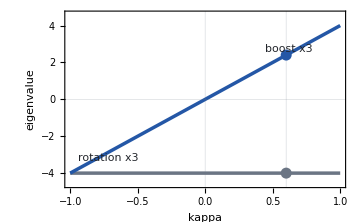
Computed herePaper narrativeLean: killing_form_diag + boost_killing_form_eq + boost_killing_nondegenerate_iff_kappa_ne_zero
Killing form self-test
Killing form self-test
-Graphics- | -Graphics-
Boost block | (2.4 | 0. | 0.
0. | 2.4 | 0.
0. | 0. | 2.4)
det(B) | -884.736
Eigenvalues | {-4.,-4.,-4.,2.4,2.4,2.4}
Readout | The boost eigenvalues are positive, so the boost block is visible and Lorentzian data can be read off. | 
The matrix view and eigenvalue plot make the paper's interpretive force visible: the rotation block stays fixed, the boost block changes sign, and the algebra becomes blind exactly at kappa = 0.

```mathematica
{-4,-4,-4,4 kappa,4 kappa,4 kappa}
```

Answer. The algebra can examine itself. The Killing form is the decisive self-test, and it becomes blind precisely when the boost sector degenerates.

## Three verdicts

Question. What does the self-test say in each regime?

The notebook keeps the paper's verdict structure intact. Negative kappa leaves no causal distinction between directions. Zero kappa preserves shape but loses the ruler and leaves absolute time as background structure. Positive kappa yields the only branch with finite real invariant speed, Lorentzian metric, and causal structure.

```mathematica
1/kappa
```

1/kappa

```mathematica
{{1,0,0,0},{0,-kappa,0,0},{0,0,-kappa,0},{0,0,0,-kappa}}
```

{{1,0,0,0},{0,-kappa,0,0},{0,0,-kappa,0},{0,0,0,-kappa}}

{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}

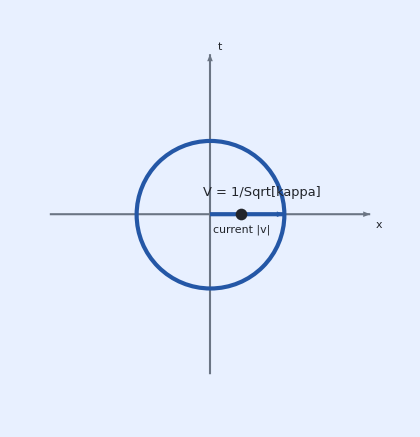
Computed herePaper narrativeLean: killing_restricts_to_metric + invariantSpeedSquared_formula + spacetime_metric_invariant + phase1_selection_summary
Velocity-space ruler and verdict board
-Graphics- | Velocity-space ruler
B(K_i, K_j) | 4 kappa delta_ij
V^2 | 1.66667
Interpretation | The Killing form fixes a preferred radius and therefore a finite invariant speed.
Three branches, three verdicts
Only the positive-kappa branch yields a finite real invariant speed, a Lorentzian metric, and causal structure without importing background geometry.
Verdict | kappa < 0 | kappa = 0 | kappa > 0
Killing form on boosts | 4 kappa < 0 | 0 | 4 kappa > 0
Invariant speed | imaginary | undefined | finite and real
Spacetime metric | Euclidean | dt^2 only | Lorentzian
Causal structure | none | none | lightcones
Space-time unification | all directions alike | impossible | complete
Background structure needed | none | yes | none
Calibration note: experiment fixes the numerical value of the invariant speed once the algebra has already selected the positive-kappa branch.
The paper's Figure 2 logic and its final comparison table are kept together: the missing ruler at kappa = 0 is not a side note, it is part of why only the positive-kappa branch fully works.

```mathematica
{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}
```

Answer. Only kappa > 0 produces a finite real invariant speed, a Lorentzian spacetime metric, and causal structure without importing background geometry by hand.

## Structure and scale

Question. What still has to be calibrated by experiment?

The paper's final distinction is preserved here: once the algebra has selected the positive-kappa branch, experiment fixes the numerical value of the invariant speed rather than the existence of such a speed. In that sense, calibration is empirical but the structural verdict is not.

Computed herePaper narrativeLean: spacetime_metric_eq_diagonal + spacetime_metric_congruent_stdLorentz_of_kappa_pos + positive_kappa_gives_finite_real_invariant_speed
Calibration after selection
Structure first, value second
If kappa > 0, then V = 1/Sqrt[kappa] is finite and real. Measuring c fixes the numerical value of kappa = 1/c^2; it does not choose whether the invariant-speed structure exists in the first place.
That is the notebook's closing claim because it is the paper's closing claim.
The value of the invariant speed is empirical calibration. The existence of a finite invariant speed is the algebra's conclusion.

Answer. Experiment calibrates the number. The algebra, if read through the Killing form, already determines that the surviving branch must carry a finite invariant speed.

## How this connects to the Lean proof

Question. Where does the formal proof live, and how does this notebook map onto it?

The crosswalk comes late on purpose. By the time it appears, the notebook should already have made the paper's geometric progression feel inevitable. Wolfram computes public-facing exact expressions and visuals; Lean formalizes the theorem statements and branch-selection results.

Computed herePaper narrativeLean: phase1_selection_summary + classification_derivation_complete + classification_derivation_complete_full
Paper -> notebook -> Lean crosswalk
Paper, notebook, and Lean crosswalk
Narrative stage | Computed / visualized here | Lean anchors | Source of authority
The postulate | Hero overview and the no-background-structure framing | OnePostulate/SpacetimeMatrices.lean; matrix_bracket_JJ; matrix_bracket_JK; matrix_bracket_KK | paper framing plus Lean entry point
What the postulate determines | Transformation simulator, Galilean limit, and the Figure 1 regime view | matrix_bracket_JJ; matrix_bracket_JK; matrix_bracket_KK; phase1_selection_summary | paper plus Lean
Can the rules examine themselves? | Bracket table, Killing form, determinant, eigenvalues, and velocity-space ruler | kinematic_bracket_table; boostCommutator_scales_with_kappa; killing_form_diag; boost_killing_nondegenerate_iff_kappa_ne_zero; killing_restricts_to_metric; invariantSpeedSquared_formula | Lean with paper interpretation
Three verdicts | Verdict board, spacetime consequences, and regime comparison | negative_kappa_no_nonzero_null_vectors; zero_kappa_selects_galilean; positive_kappa_selects_lorentz; positive_kappa_gives_finite_real_invariant_speed; spacetime_metric_invariant | Lean plus paper verdict
Structure and scale | Calibration note and Lorentz congruence preview | spacetime_metric_eq_diagonal; spacetime_metric_congruent_stdLorentz_of_kappa_pos; classification_derivation_complete_full | paper plus Lean
The crosswalk is concise rather than exhaustive. Its job is to point a reader from the paper's rhetorical stages to the local formal surface without pretending the notebook is the proof.

Answer. The formal proof lives in the local Lean modules. The notebook computes, visualizes, and narrates the same architecture without widening the proof surface.

## What is computed here vs proved in Lean

Question. Which claims are computed here, and which are proved elsewhere?

The notebook keeps the proof boundary visible throughout with inline badges, but it closes with an explicit summary as well. This matters because the notebook is designed to persuade by making structure visible, not by silently upgrading itself into a proof assistant.

Category | What belongs there
Computed or visualized here | Exact transformation-law limits, the shared dynamic panels, the Killing-form eigenvalue and determinant checks, the velocity-space ruler story, the verdict board, and the Lorentz congruence calculation for positive kappa.
Formally proved in Lean | The local theorem anchors, bracket identities, invariant-form theorems, and branch-selection theorems exposed through OnePostulate.lean, OnePostulateFull.lean, and the modules under OnePostulate/.
Interpretive narrative from the paper | Why the relativity principle forbids imported background structure, why kappa = 0 loses the ruler, why only kappa > 0 yields causal structure, and why experiment calibrates value rather than existence.

Answer. This notebook computes and visualizes exact expressions already present in the local development. Lean remains the proof authority, and the paper remains the source of the public-facing interpretive narrative.